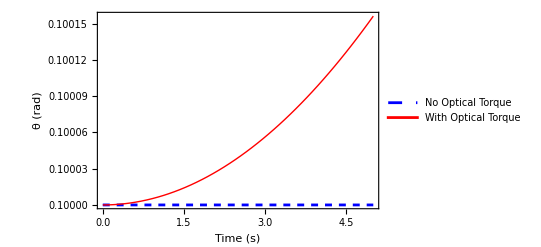

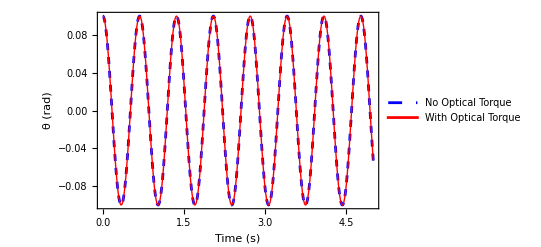

```mathematica
(*1. Constant Parameters*)
ρ=2070;
r1=4.5*10^-3;
r2=5.5*10^-3;
T=1.1*10^-3;
M=Pi ρ (r2^2-r1^2) T;
Ic=1/2 M (r1^2+r2^2);

c=3*10^8;
lambda=1.064*10^-6;
ωLight=2 Pi c/lambda;
P=10;
α=1;

(*Pre-calculate the constant Laser Acceleration*)
Aopt=(4 α P)/(ωLight Ic);
ωo=9.2224;
(*-----------------------------------------------------------------*)
(*2. THE SOLVERS*)
(*Start all simulations at theta=0.1 with zero initial velocity*)

(*Scenario 1a:Flat Umag,No Laser (ωo=0,Aopt=0)*)
sol1a=DSolveValue[{θ''[t]==0,θ[0]==0.1,θ'[0]==0},θ[t],t];

(*Scenario 1b:Flat Umag,With Laser (ωo=0,Aopt ON)*)
sol1b=DSolveValue[{θ''[t]==Aopt,θ[0]==0.1,θ'[0]==0},θ[t],t];

(*Scenario 2a:Harmonic Umag,No Laser (ωo ON,Aopt=0)*)
sol2a=DSolveValue[{θ''[t]==-ωo^2 θ[t],θ[0]==0.1,θ'[0]==0},θ[t],t];

(*Scenario 2b:Harmonic Umag,With Laser (ωo ON,Aopt ON)*)
sol2b=DSolveValue[{θ''[t]==Aopt-ωo^2 θ[t],θ[0]==0.1,θ'[0]==0},θ[t],t];

(*-----------------------------------------------------------------*)
(*3. PLOTTING THE 4 GRAPHS*)

(*Graph 1:The Flat Potential Comparison*)
Plot[{sol1a,sol1b},{t,0,5},PlotStyle->{{Blue,Dashed},{Red,Thick}},PlotLegends->{"No Optical Torque","With Optical Torque"},Frame->True,FrameLabel->{"Time (s)","θ (rad)"}]

(*Graph 2:The Harmonic Trap Comparison*)
Plot[{sol2a,sol2b},{t,0,5},PlotStyle->{{Blue,Dashed},{Red,Thick}},PlotLegends->{"No Optical Torque","With Optical Torque"},Frame->True,FrameLabel->{"Time (s)","θ (rad)"}]
```

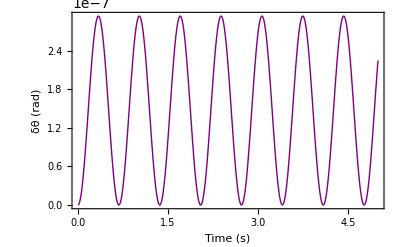

```mathematica
(*The "Microscope View":Subtracting the baseline to see the laser*)Plot[sol2b-sol2a,{t,0,5},PlotRange->All,PlotStyle->{Purple,Thick},Frame->True,FrameLabel->{"Time (s)","δθ (rad)"}]
```

```mathematica
imgRes=400;

(*COMMON STYLE OPTIONS*)
axisStyle=Directive[Black,16];
labelStyle=Directive[Black,18];
legendStyle=Directive[Black,16];

(*1) Flat potential comparison*)
g1=Plot[{sol1a,sol1b},{t,0,5},PlotStyle->{{Blue,Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},Frame->True,FrameStyle->axisStyle,FrameTicksStyle->axisStyle,FrameLabel->{Style["Time (s)",labelStyle],Style["\!\(\*SubscriptBox[\(θ\), \(z\)]\) (rad)",labelStyle]},Background->White,BaseStyle->axisStyle,PlotRangePadding->Scaled[0.03],ImageSize->500,PlotLegends->Placed[LineLegend[{Style["No Optical Torque",legendStyle],Style["With Optical Torque",legendStyle]},LegendLayout->"Column",LegendFunction->(Framed[#,Background->White,FrameStyle->None,RoundingRadius->0]&)],{1.05,0.5}   (*just outside the right edge,vertically centered*)]];

(*2) Harmonic trap comparison*)
g2=Plot[{sol2a,sol2b},{t,0,5},PlotStyle->{{Blue,Dashed,Thickness[0.004]},{Red,Thickness[0.004]}},Frame->True,FrameStyle->axisStyle,FrameTicksStyle->axisStyle,FrameLabel->{Style["Time (s)",labelStyle],Style["\!\(\*SubscriptBox[\(θ\), \(z\)]\) (rad)",labelStyle]},Background->White,BaseStyle->axisStyle,PlotRangePadding->Scaled[0.03],ImageSize->500,PlotLegends->Placed[LineLegend[{Style["No Optical Torque",legendStyle],Style["With Optical Torque",legendStyle]},LegendLayout->"Column",LegendFunction->(Framed[#,Background->White,FrameStyle->None,RoundingRadius->0]&)],{1.05,0.5}]];

(*3) Microscope view:difference*)
g3=Plot[sol2b-sol2a,{t,0,5},PlotStyle->{Directive[Purple,Thickness[0.004]]},Frame->True,FrameStyle->axisStyle,FrameTicksStyle->axisStyle,FrameLabel->{Style["Time (s)",labelStyle],Style["\!\(\*Delta\)θ\!\(\*SubscriptBox[\(_\), \(z\)]\) (rad)",labelStyle]},Background->White,BaseStyle->axisStyle,PlotRangePadding->Scaled[0.03],ImageSize->500];

(*EXPORTS*)
Export["flat_potential.png",g1,"PNG",ImageResolution->imgRes];
Export["harmonic_trap.png",g2,"PNG",ImageResolution->imgRes];
Export["microscope_view.png",g3,"PNG",ImageResolution->imgRes];
```